## Контрольная работа №1 Студента 3 курса 6 группы Дунаева Виктора Андреевича Вариант 4

## Task 1

```mathematica
(* {{-1/10,0,1/10,1/5,3/10,2/5},{0,1/9,2/9,1/3,4/9},{1/8,1/4,3/8,1/2},{2/7,3/7,4/7},{1/2,2/3},{4/5}}*)
(*{{4/5},{2/3,1/2},{4/7,3/7,2/7},{1/2,3/8,1/4,1/8},{4/9,1/3,2/9,1/9,0},{2/5,3/10,1/5,1/10,0,-1/10}} *)
(* {{-1/5,0,1/5,2/5,3/5,4/5},{-1/6,0,1/6,1/3,1/2},{-1/7,0,1/7,2/7},{-1/8,0,1/8},{-1/9,0},{-1/10}}*)
```

```mathematica
Table[j/(10-i),{i,0,5,1},{j,i-1,4,1}]
```

{{-1/10,0,1/10,1/5,3/10,2/5},{0,1/9,2/9,1/3,4/9},{1/8,1/4,3/8,1/2},{2/7,3/7,4/7},{1/2,2/3},{4/5}}

```mathematica
Table[j/(10-i),{i,5,0,-1},{j,4,i-1,-1}]
```

{{4/5},{2/3,1/2},{4/7,3/7,2/7},{1/2,3/8,1/4,1/8},{4/9,1/3,2/9,1/9,0},{2/5,3/10,1/5,1/10,0,-1/10}}

```mathematica
Table[i/j,{j,5,10,1},{i,-1,9-j,1}]
```

{{-1/5,0,1/5,2/5,3/5,4/5},{-1/6,0,1/6,1/3,1/2},{-1/7,0,1/7,2/7},{-1/8,0,1/8},{-1/9,0},{-1/10}}

## Task 2

```mathematica
m=(4 z^2+4  x  y  z-2  x^2 z+6  y  z)^4
```

(-2 x^2 z+6 y z+4 x y z+4 z^2)^4

```mathematica
Factor[m]
```

16 (x^2-3 y-2 x y-2 z)^4 z^4

```mathematica
Collect[Expand[m],y]
```

16 x^8 z^4-128 x^6 z^5+384 x^4 z^6-512 x^2 z^7+256 z^8+y^4 (1296 z^4+3456 x z^4+3456 x^2 z^4+1536 x^3 z^4+256 x^4 z^4)+y^3 (-1728 x^2 z^4-3456 x^3 z^4-2304 x^4 z^4-512 x^5 z^4+3456 z^5+6912 x z^5+4608 x^2 z^5+1024 x^3 z^5)+y^2 (864 x^4 z^4+1152 x^5 z^4+384 x^6 z^4-3456 x^2 z^5-4608 x^3 z^5-1536 x^4 z^5+3456 z^6+4608 x z^6+1536 x^2 z^6)+y (-192 x^6 z^4-128 x^7 z^4+1152 x^4 z^5+768 x^5 z^5-2304 x^2 z^6-1536 x^3 z^6+1536 z^7+1024 x z^7)

```mathematica
Collect[Expand[m],x,Simplify]
```

16 x^8 z^4-128 x^7 y z^4-128 x^5 y (-9 y+4 y^2-6 z) z^4+64 x^6 (-3 y+6 y^2-2 z) z^4+64 x^2 (-3 y+6 y^2-2 z) z^4 (3 y+2 z)^2+128 x y z^4 (3 y+2 z)^3+16 z^4 (3 y+2 z)^4+32 x^4 z^4 (-72 y^3+8 y^4+y^2 (27-48 z)+36 y z+12 z^2)+128 x^3 y z^4 (12 y^3-36 y z-12 z^2+y^2 (-27+8 z))

## Task 3

```mathematica
(* С помощью соответствующей встроенной функции Mathematica разложить в ряд Фурье по синусам и косинусам следующие функции:
1) f(t)=t^4-2t+3,t∈[-L,L],L>0;sin⁡〖(πn/L t),〗 cos⁡〖(πn/L t) 〗.Разлагать до n=3.
*)
```

```mathematica
function[_x] := x^4-2x+3
```

```mathematica
(* N - element *)
```

```mathematica
FourierCosCoefficient[x^4-2x+3,x,n]
```

-(48 (-1)^n)/n^4+(4 (1+(-1)^(1+n)+2 (-1)^n π^3))/(n^2 π)

```mathematica
FourierSinCoefficient[x^4-2x+3,x,n]
```

(-48 (-1+(-1)^n)+24 (-1)^n n^2 π^2+n^4 (6-6 (-1)^n+4 (-1)^n π-2 (-1)^n π^4))/(n^5 π)

```mathematica
(* Cos *)
```

```mathematica
FourierCosCoefficient[x^4-2x+3,x,3]
```

(8 (3+2 π-3 π^3))/(27 π)

```mathematica
FourierCosCoefficient[x^4-2x+3,x,2]
```

-3+2 π^2

```mathematica
FourierCosCoefficient[x^4-2x+3,x,1]
```

8 (6+1/π-π^2)

```mathematica
(* Sin *)
```

```mathematica
FourierSinCoefficient[x^4-2x+3,x,3]
```

2/81 (-54+178/π-36 π+27 π^3)

```mathematica
FourierSinCoefficient[x^4-2x+3,x,2]
```

2+3 π-π^3

```mathematica
FourierSinCoefficient[x^4-2x+3,x,1]
```

2 (-2+54/π-12 π+π^3)

```mathematica
(* 2) f(x,t)=(t-2)^2 arcsin⁡(x-4),sin⁡〖πnt,cos⁡〖πnt,t∈[-π,π],n=3.〗 〗 При этом функцию arcsin⁡(x-4) разложить в ряд Тейлора по степеням x-5 до 5-й производной.*)
```

## Task 4

```mathematica
(* Изобразить графически и подсчитать площадь следующих областей.1) Область,ограниченная кривыми x^2+y^2=1,y=ln⁡x+1⁄2,x=(-1)⁄2,x=3⁄4,y=0 *)
```

```mathematica
R= ImplicitRegion[{y==Sqrt[1-x^2],y==Log[x]+ (1/2),x==-(1/2),x==(3/4),y==0},{x,y}]
```

ImplicitRegion[y==√(1-x^2)&&y==1/2+Log[x]&&x==-1/2&&x==3/4&&y==0,{x,y}]

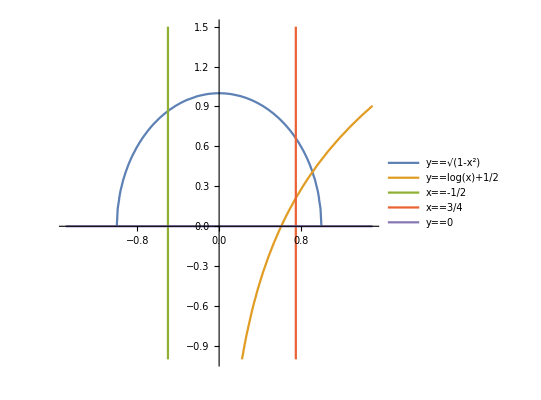

```mathematica
g1 = ContourPlot[{y==Sqrt[1-x^2],y==Log[x]+ (1/2),x==-(1/2),x==(3/4),y==0},{x,-1.5,1.5},{y,-1,1.5},Frame->False,Axes->True,PlotLegends->"Expressions"]
```

Less::nord: Invalid comparison with 0.+1.11782 ⅈ attempted.

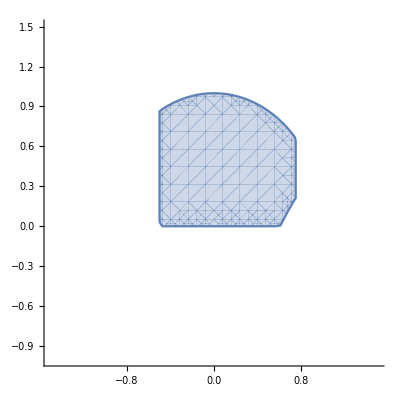

```mathematica
g2=RegionPlot[y<Sqrt[1-x^2]&&x*ⅇ^(1/2)<Exp[y]&&x>(-1/2)&&x<(3/4)&&y>0,{x,-1.5,1.5},{y,-1,1.5},Frame->False,Axes->True]
```

```mathematica
p1={(-1/2),0}
p2={(-1/2),Sqrt[3/4]}
```

{-1/2,0}

{-1/2,(√3)/2}

```mathematica
p3 = {0.6,0}
```

{0.6,0}

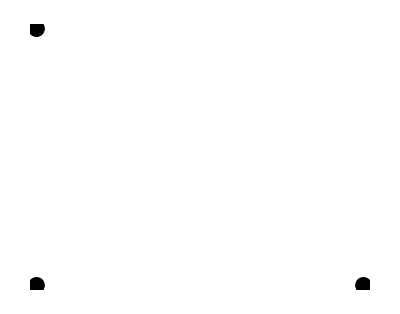

```mathematica
g3=Graphics[{PointSize[0.03],Point[{p1,p2,p3},VertexColors->{Red, Green, Blue}]}]
```

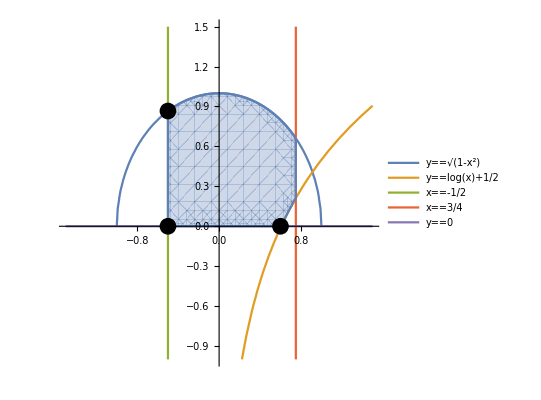

```mathematica
Show[g1,g2,g3]
```

```mathematica
(* Считаем значение интеграла *)
```

```mathematica
∫_-0.5^0.6 (Sqrt@(1-x^2))ⅆx+∫_0.6^0.75 (Sqrt@(1-x^2)-Log[x]-1/2)ⅆx//N
```

1.13464

## Task 5